# Presentation Quality Graphs

RockSprings Plot

Read::readn: Invalid real number found when reading from "C:\\Users\\Sam\\Desktop\\Thesis Work\\irene_norivers\\spinup\\tarboro_wse_median_spinup.txt".

General::stop: Further output of Read :: readn will be suppressed during this calculation.

ListPlot::prng: Value of option PlotRange -> {{3521923200, 3526243200}, {-1 + Min[1.11, 3.28084\ $Failed], 1 + Max[18.92, 3.28084\ $Failed]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

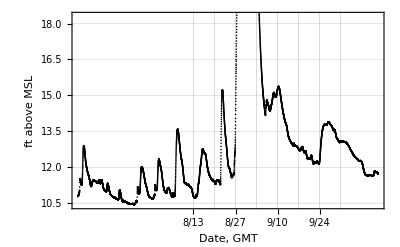

{{Tue 5 Jul 2011 19:00:00,3.28084 $Failed},{Tue 30 Aug 2011 23:45:00,28.24},{-1300.,-28.24+3.28084 $Failed}}

```mathematica
data=plotgauge["irene_norivers","tarboro"];
data[[1]]
data[[2;;4]]
```

AbsoluteTime::ambig: Warning: the interpretation of the string "8/10/2011 0:00" as a date is ambiguous.

AbsoluteTime::ambig: Warning: the interpretation of the string "8/10/2011 0:15" as a date is ambiguous.

AbsoluteTime::ambig: Warning: the interpretation of the string "8/10/2011 0:30" as a date is ambiguous.

General::stop: Further output of AbsoluteTime :: ambig will be suppressed during this calculation.

Read::readn: Invalid real number found when reading from "C:\\Users\\Sam\\Desktop\\Thesis Work\\irene_norivers\\spinup\\rock_springs_wse_median_spinup.txt".

General::stop: Further output of Read :: readn will be suppressed during this calculation.

ListPlot::prng: Value of option PlotRange -> {{3521923200, 3526243200}, {-1 + Min[0.29, 3.28084\ $Failed], 1 + Max[15.56, 3.28084\ $Failed]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

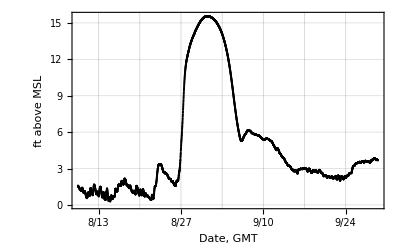

{{Tue 5 Jul 2011 19:00:00,3.28084 $Failed},{Wed 31 Aug 2011 20:00:00,15.56},{-1400.,-15.56+3.28084 $Failed}}

```mathematica
data=plotgauge["irene_norivers","rock_springs"];
data[[1]]
data[[2;;4]]
```

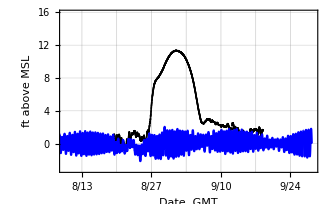

{{Tue 30 Aug 2011 04:00:00,2.03913},{Thu 1 Sep 2011 12:30:00,11.35},{-57.,-9.31087}}

```mathematica
data=plotgauge["irene_norivers","greenville"];
data[[1]]
data[[2;;4]]
```

AbsoluteTime::ambig: Warning: the interpretation of the string "7/6/2011 0:00" as a date is ambiguous.

AbsoluteTime::ambig: Warning: the interpretation of the string "7/6/2011 0:15" as a date is ambiguous.

AbsoluteTime::ambig: Warning: the interpretation of the string "7/6/2011 0:30" as a date is ambiguous.

General::stop: Further output of AbsoluteTime :: ambig will be suppressed during this calculation.

Read::readn: Invalid real number found when reading from "C:\\Users\\Sam\\Desktop\\Thesis Work\\irene_norivers\\spinup\\grimesland_wse_median_spinup.txt".

General::stop: Further output of Read :: readn will be suppressed during this calculation.

ListPlot::prng: Value of option PlotRange -> {{3521923200, 3526243200}, {-1 + Min[-1.17, 3.28084\ $Failed], 1 + Max[5.41, 3.28084\ $Failed]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

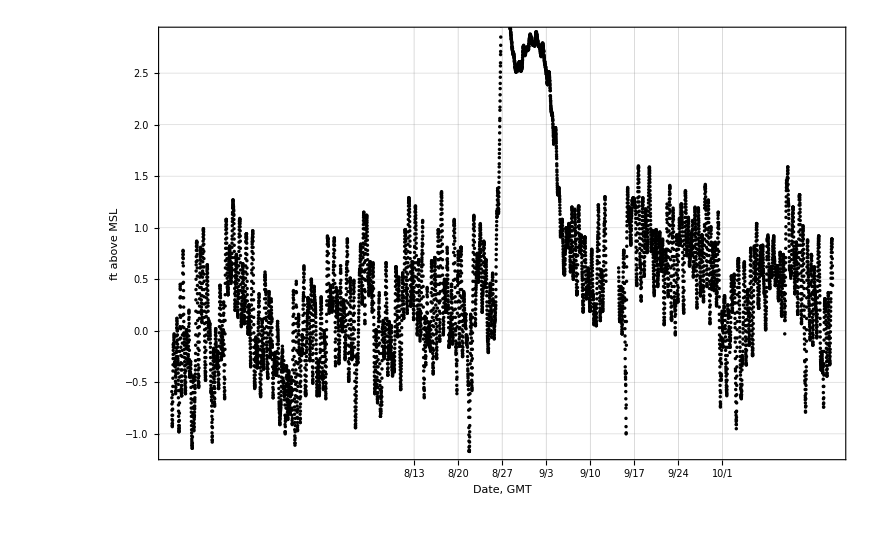

{{Tue 5 Jul 2011 19:00:00,3.28084 $Failed},{Sat 27 Aug 2011 14:15:00,5.41},{-1300.,-5.41+3.28084 $Failed}}

```mathematica
data=plotgauge["irene_norivers","grimesland"];
data[[1]]
data[[2;;4]]
```

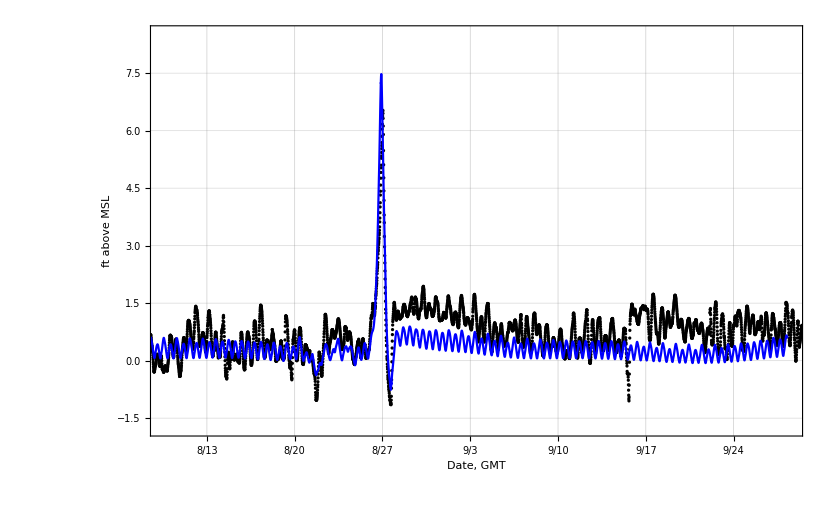

{{Sat 27 Aug 2011 09:45:00,7.47651},{Sat 27 Aug 2011 12:45:00,6.53},{-3.,0.946506}}

```mathematica
data=plotgauge["irene_norivers","pamlico"];
data[[1]]
data[[2;;4]]
```

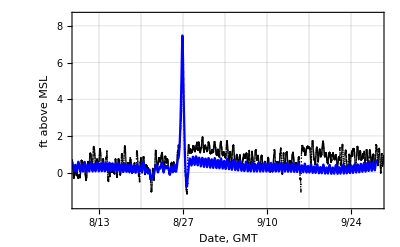

{{Sat 27 Aug 2011 09:45:00,7.47651},{Sat 27 Aug 2011 12:45:00,6.53},{-3.,0.946506}}

```mathematica
data=plotgauge["irene_norivers","pamlico"];
data[[1]]
data[[2;;4]]
noriv=data[[6]];

data=plotgauge["irene","pamlico"];
riv=data[[6]];
```

```mathematica
Dimensions[riv]
Dimensions[noriv]
```

{28800,2}

{24480,2}

```mathematica
diff=Transpose[riv[[1;;24480]]][[2]]-Transpose[noriv][[2]];
```

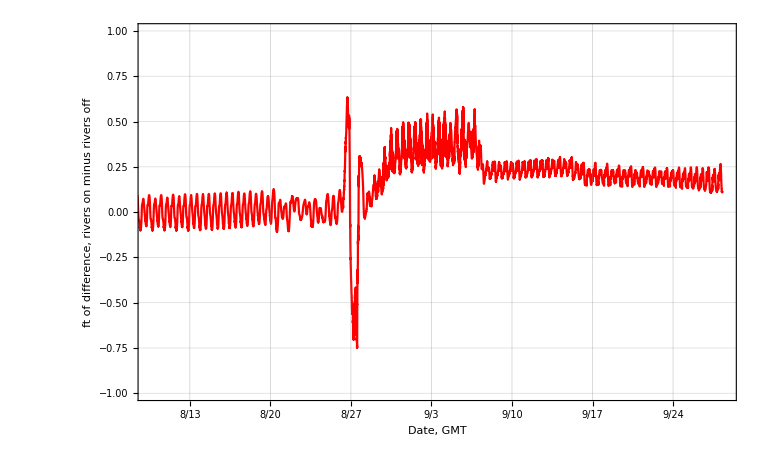

```mathematica
diffscatter=Transpose[Table[{Transpose[noriv][[1]],diff}]];

start2=AbsoluteTime[{"8/10/2011",{"Month","Day","Year"}}];
end=start2+(24*60*60*50);

scatterplot[diffscatter,start2,end,-1,1,"ft of difference, rivers on minus rivers off","Date, GMT","Pamlico at Washington 02084472",7,True,Red]
```

```mathematica
dsbc=Table[{DateString[noriv[[i,1]]],noriv[[i,2]]},{i,1,Length[noriv]}];
Export["C:\\Users\\Sam\\Desktop\\Thesis Work\\irene_norivers\\irene_norivers_ds_bc.csv",dsbc]
```

C:\Users\Sam\Desktop\Thesis Work\irene_norivers\irene_norivers_ds_bc.csv